```mathematica
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
Needs["ErrorBarPlots`"];
dataplot = ErrorBarPlots`ErrorListPlot[data];
Print[dataplot];
fit=FindFit[Table[data[[i,1]],{i,1,Length[data]}],a x^2+b x+c,{a,b,c},x];
Print[fit];
fitplot=Plot[F[x]/.fit,{x,0,35}];
Print[fitplot];
Show[dataplot,fitplot]
```

{{{1,10.9474},{2,57.5007},{3,103.937},{4,164.375},{5,212.468},{6,238.857},{7,296.325},{8,360.051},{9,394.261},{10,430.037},{11,506.287},{12,546.761},{13,588.802},{14,632.41},{15,677.585},{16,724.328},{17,772.637},{18,822.515},{19,873.96},{20,926.973}},{{1,20.0677},{2,219.325},{3,335.336},{4,402.701},{5,438.727},{6,515.467},{7,556.182},{8,598.461},{9,642.304},{10,687.712},{11,734.684},{12,783.223},{13,833.326},{14,884.995},{15,938.231}},{{1,31.9045},{2,226.867},{3,312.419},{4,411.965},{5,448.262},{6,525.533},{7,566.508},{8,609.045},{9,653.142},{10,698.802},{11,746.023},{12,794.808},{13,845.156},{14,897.067},{15,950.542}},{{1,46.4586},{2,235.014},{3,321.512},{4,386.923},{5,458.543},{6,536.382},{7,577.636},{8,620.447},{9,664.817},{10,710.745},{11,758.233},{12,807.28},{13,857.888},{14,910.057},{15,963.787}},{{1,63.7305},{2,271.333},{3,331.207},{4,397.256},{5,469.496},{6,507.941},{7,547.937},{8,589.486},{9,632.588},{10,677.245},{11,723.458},{12,771.227},{13,820.552},{14,871.435},{15,923.877}},{{1,83.7203},{2,226.445},{3,310.399},{4,408.172},{5,443.846},{6,519.826},{7,560.136},{8,601.995},{9,645.403},{10,690.363},{11,736.874},{12,784.938},{13,834.555},{14,885.727},{15,938.455}},{{1,106.428},{2,235.725},{3,320.795},{4,385.15},{5,455.643},{6,493.198},{7,572.931},{8,615.113},{9,658.841},{10,704.116},{11,750.939},{12,799.311},{13,849.233},{14,900.707},{15,953.733}},{{1,131.854},{2,219.715},{3,331.657},{4,396.75},{5,467.959},{6,505.863},{7,545.303},{8,586.282},{9,628.8},{10,672.86},{11,718.462},{12,765.609},{13,814.302},{14,864.541},{15,916.328},{16,969.664}},{{1,159.999},{2,229.414},{3,312.308},{4,408.814},{5,444.025},{6,519.028},{7,558.826},{8,600.156},{9,643.022},{10,687.425},{11,733.367},{12,780.849},{13,829.873},{14,880.44},{15,932.551}}}

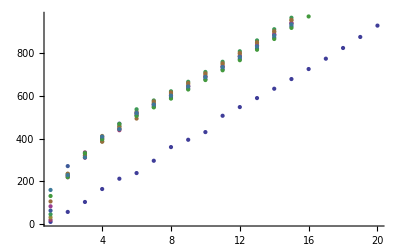

```mathematica
ListPlot[Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}]]
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.